# Numerical Phase Shift Method

```mathematica
SetOptions[Notebooks["phaseShiftSolver.nb"][[1]],AutoGeneratedPackage->Automatic]
```

## Description

The algorithm below is organized as follow:
- solverDE finds asymptotic numerical solutions
- fitExp fits the numerical solution return by solverDE in terms of function {Exp[ⅈ  p  x], Exp[-ⅈ  p  x] }
- findRealPhase finds the phaseshift from the coefficients (assumed to be real) from fitExp
- findComplexPhase finds the complex phaseshift for complex coefficients from fitExp
- dataNoJump corrects the π-jump artefact in phaseshifts returned by phaseTable
- phaseTable puts together solverDE and fitExpPhase to return a list of phaseshifts for different wavefunctions
- pPhaseTable returns the table {p, phaseshifts} corrected from π jumps for different wavefunctions

So, pPhaseTable is the final function to call.

See their usages for more details.

Note that the phase-shift method does not depend on constant phase-shifts (see section below for details), hence our code will not track the constant terms.

## Phase-shift method

This method solves functional determinants.

### 2nd order ODE: Schrödinger problems

Solution:
	A=tr log O/O_reg=-∫_0^∞ ⅆp/π δ(p)+divergent term

#### Setting

Consider O=ω^2+H, where
	 H[x,∂_x,(∂_x)^2]Ψ(x)=-p^2Ψ(x) 
such that at x>>1, it reduces to a plane wave equation
	∂^2 Ψ(x)=-p_0^2Ψ(x)	
Then, we can parametrize the wave function as
	Ψ(x)=A(p)sin(p x+δ(p)), x>>1
	A, δ can be complex

#### Initial condition, scalar product and hemiticity

We impose the initial condition such that we select the normalizable mode with respect to the scalar product
	⟨Ψ ,Ψ⟩=∫_1^∞ ⅆx g(x) Ψ^*(x)Ψ(x)
	
The operator O must be Hermitian with respect to this scalar product, i.e.
	⟨O Ψ_1,Ψ_2⟩=⟨Ψ_1,O^* Ψ_2⟩, O^*=O
in order to ensure real eigenvalues.

In practice, we can absorb the metric factor by rescaling the fields.
The most general Hermitian form for an operator with respect to the flat metric is:
	O=d/(d x)r(x)d/(d x)+potential
     =r(x)d^2/(d x^2)+r'(x)d/(d x)+potential

#### Quantization condition

Artificial boundary conditions 
	Ψ(R)=0; R→ ∞ (so we can approximate the sum by an integral)
to quantize the momentum:
	p R+δ(p)=π n → p_n 
For the asymptotic operator, δ(p)=0, so p_(0n)=(π n)/R

#### Determinant before ω integration

A=tr log O/O_reg=∫_(-∞)^∞ ⅆω/(2π)D
	D=∑_n log (ω^2+p_n^2)-∑_n log (ω^2+(p_(0n))^2)

In terms of the momentum:
	ⅆp R+δ'(p)ⅆp=π ⅆn→ ⅆn/ⅆp=R/π+(δ'(p))/π

D=∫_0^∞ ⅆp( ⅆn/ⅆp -ⅆn/ⅆp[δ(p)=0])log (ω^2+p^2)
    =∫_0^∞ ⅆp(δ'(p))/π log (ω^2+p^2)
    =[(δ(p))/π log (ω^2+p^2)]_0^∞-∫_0^∞ ⅆp(δ(p))/π(2p)/(ω^2+p^2)

D is obviously invariant under a constant shift: δ → δ + const
	D=[(δ(p)+const)/π log (ω^2+p^2)]_0^∞-∫_0^∞ ⅆp(δ(p))/π(2p)/(ω^2+p^2)-[const/π log (ω^2+p^2)]_0^∞=[(δ(p))/π log (ω^2+p^2)]_0^∞-∫_0^∞ ⅆp(δ(p))/π(2p)/(ω^2+p^2)

```mathematica
Integrate[1/π(2p)/(ω^2+p^2),p]
```

Log[p^2+ω^2]/π

#### Solution

A=-∫_(-∞)^∞ ⅆω/(2π)∫_0^∞ ⅆp(δ(p))/π(2p)/(ω^2+p^2)+surface term=-∫_0^∞ ⅆp/π δ(p)+surface term

since:

```mathematica
Assuming[p>0,∫_(-∞)^∞ 1/(2π)(2p)/(ω^2+p^2)ⅆω]
```

1

A=∫_(-∞)^∞ ⅆω/(2π)∫_0^∞ ⅆp(δ'(p))/π log (ω^2+p^2)
     =∫_0^∞ ⅆp(δ'(p))/π∫_(-∞)^∞ ⅆω/(2π)(log (1+p^2/ω^2)+log(ω^2))
     =∫_0^∞ ⅆp(δ'(p))/π p + kinetical divergence
     =[(δ(p))/π p]_0^∞-∫_0^∞ ⅆp(δ(p))/π + kinetical divergence

```mathematica
Assuming[p>0,∫_(-∞)^∞ 1/(2π)Log[1+p^2/ω^2]ⅆω]
```

p

### 1st order ODEs

Solution:
	A=tr log F/F_reg=-∫_0^∞ ⅆp/(2π)(α^2 p)/(√(m^2+(α p)^2)){δ_+(p) +δ_-(p)}+divergent surface term

#### Strategy for the general case

Given an eigenvalue problem O Ψ= λ Ψ, when O is a matrix.  The strategy is to separate the part proportional to the identity from the rest:
O=λ_1 Id+O_2
Then, we can solve the eigenvalue problem for the O_2 operator:
O_2 Ψ=λ_2 Ψ
and the total eigenvalue will be λ=λ_1+λ_2.

#### Setting

Consider the Dirac representation for Schrödinger operators. 
That is, the operator 
	F=(m+ⅈ ω+a[x] | L_1[x,∂_x]
L_2[x,∂_x] | m-ⅈ ω+b[x])
where L_1^†=-L_2, i.e. the off-diagonal terms are anti-Hermitian with respect to its scalar product,
such that when x>>1, it reduces to a Dirac operator of the form:
	F_reg=(m+ⅈ ω | α∂_x
α ∂_x | m-ⅈ ω) ,  α is a number

We choose initial conditions such that the modes are normalizable with respect to the metric.	
The rescaling to a flat metric is done by the prescription:
	F → g^(1/2)F g^(-1/2)
∂_x → ∂_x +(g(x))^(1/2)∂_x (g(x))^(-1/2)
where g is the metric factor.

#### Eigenvalue problem for a matrix operator

Let us decompose F as
	F[ω]=F[ω=0] +ⅈ ω σ_3
 multiply it by σ_3
	σ_3 F[ω]=ⅈ ω Id + σ_3 F[ω=0]
the eigenvalue problem to solve is
	(σ_3 F[ω=0]-λ Id) Ψ =0   → eigenvalues: λ_± and eigenvectors Ψ_±
which is equivalent of solving
	(F[ω=0]-λ σ_3) Ψ =0         → eigenvalues: λ_± and eigenvectors Ψ_±
Notice that -λ is playing the same role as ⅈ ω in the original problem.  The determinant will be
	det F=-det (σ_3 F)=-det  (ⅈ ω+λ_+ | 0
0 | ⅈ ω+λ_-)

#### Parametrize the eigenvalues

For its asymptotic operator, 
	F_reg=(m+ⅈ ω | α∂_x
α ∂_x | m-ⅈ ω) 
 the eigenvalue problem ((F̃)_reg-λ0 σ_3) Ψ =0, for Ψ=exp(ⅈ α p τ), gives 
	det(m-λ0 | ⅈ α p0
ⅈ α p0 | m+λ0) =m^2-λ0^2+(α p0)^2=0→ λ0_±=±√(m^2+(α p0)^2)
Hence,λ_±→ λ0_± in the asymptotic limit, and we can parametrize
	 λ_±=±√(m^2+(α p)^2)

#### Derive the determinant

We must keep the 2 phases related to the 2 eigenvalues separately since they are in general different, i.e. δ_+≠δ_-:

A=∫_(-∞)^∞ ⅆω/(2π)D	
	D=∑_n log((ⅈ ω+√(m^2+(α p_n)^2))/(ⅈ ω+√(m^2+(α p0_n)^2))) +log((ⅈ ω-√(m^2+(α p_n)^2))/(ⅈ ω-√(m^2+(α p0_n)^2)))
	   =∫_0^∞ ⅆp ( ⅆn/ⅆp -ⅆn/ⅆp[δ_+(p)=0]) log(ⅈ ω+√(m^2+(α p)^2)) + ( ⅆn/ⅆp -ⅆn/ⅆp[δ_-(p)=0]) log(ⅈ ω-√(m^2+(α p)^2)) 
	   =∫_0^∞ ⅆp (δ'_+(p))/π log(ⅈ ω+√(m^2+(α p)^2)) + (δ'_-(p))/π log(ⅈ ω-√(m^2+(α p)^2))  
	   =surface terms-∫_0^∞ ⅆp/π(α^2 p)/(√(m^2+(α p)^2))((δ_+(p))/(√(m^2+(α p)^2)+ⅈ ω) -(δ_-(p))/(-√(m^2+(α p)^2)+ⅈ ω))

Let’s commute the ω-integral with the p-integral and perform the former:
∫_(-∞)^∞ ⅆω/(2π)((δ_+(p))/(√(m^2+(α p)^2)+ⅈ ω) -(δ_-(p))/(-√(m^2+(α p)^2)+ⅈ ω))=(δ_+(p) +δ_-(p))/2
		∫_(-∞)^∞ ⅆω/(2π ⅈ) (δ_±(p))/(ω+ ∓ ⅈ λ)=-∫_C ⅆω/(2π ⅈ) (δ_±(p))/(ω+ ∓ ⅈ λ)( i.e. we choose the close contour to not include the pole)
		∫_C ⅆω/(2π ⅈ) 1/(ω+ ∓ ⅈ λ)=∫_0^(∓π) (R ⅇ^(ⅈ θ)ⅈⅆθ)/(2π ⅈ) 1/(R ⅇ^(ⅈ θ)+ ∓ ⅈ λ)={ for R→ ∞ and >> λ } =∫_0^(∓π) ⅆθ/(2π) =∓1/2  
	In conclusion
		 ∫_(-∞)^∞ ⅆω/(2π ⅈ) (δ_±(p))/(ω+ ∓ ⅈ λ)=+±1/2δ_±(p); λ=√(m^2+(α p)^2)

Final solution:
	A=-∫_0^∞ ⅆp/π(α^2 p)/(√(m^2+(α p)^2))(δ_+(p) +δ_-(p))/2+divergent surface term

```mathematica
D[Log[ⅈ ω-√(1+(α p)^2)],p]
```

-(p α^2)/(√(1+p^2 α^2) (-√(1+p^2 α^2)+ⅈ ω))

## Code

```mathematica
BeginPackage["phaseShiftSolver`"]
solverDE::usage="solverDE[DE, Ψs, {x, min}, p] uses NDSolve to solve eigenvalue problems that asymptotically reduce to plane wave systems with eigenvalue p. It returns a matrix of solutions for Ψs at positions in the interval [min, min+3(2  π)/p].  ";
fitExp::usage="fitExp[data,p][x] fits the data with exponentials:
	C[1] Exp[ⅈ p x] + C[2] Exp[-ⅈ p x] ";
findRealPhase::usage="findRealPhase[data,p] returns the phase from fitExp, assuming its coefficients are real.";
findComplexPhase::usage="findComplexPhase[data,p] returns the phase from fitExp, assuming its coefficients are imaginary.";
dataNoJump::usage="dataNoJump[data] returns the data without π jumps";
phaseTable::usage="phaseTable[DE,Ψs,{x,xmin},{p,pRange}][[i]] returns a list of phases for the given range of ps for Ψs[[i]]. Note: xmin should be large enough such that xmin*p>>1, which is the limit where the phase-shift method works. ";
pPhaseTable::usage="pPhaseTable[DE,Ψs,{x,xmin},{p,pRange}][[i]] returns a list of {p, phase} for Ψs[[i]]. Note: xmin should be large enough such that xmin*p>>1, which is the limit where the phase-shift method works.";
testFitting::usage="testFitting[DE,ϕ,{x,min},p] shows the plot of the numeric result and the fit with the derived phaseshift.";

Begin["`Private`"]
Needs["commons`"]
```

```mathematica
solverDE[DE_,Ψs_List,{x_?notNumericQ,min_?NumericQ},p_?NumericQ]:=Module[{len,waveL,max,steps,interpolations,X,Y},
waveL=N[(2π)/p];max=min+3waveL;steps=3waveL/50.;
len=Length@Ψs;
interpolations=Ψs/.Flatten@NDSolve[DE,Ψs,{x,min,max}, Method->"StiffnessSwitching"];
X=Range[min,max,steps];
Y=mapParallel[interpolations,X];
Transpose@{X,#}&/@Y
]

(**************************************************************************************)
fitExp[data_List,p_?NumericQ][x_]:=Fit[data,{Exp[ⅈ  p x],Exp[-ⅈ p x ]},x];

findRealPhase[data_List,p_?NumericQ]:=Module[{a,x},
{a}=Coefficient[fitExp[data,p][x],{Exp[ⅈ p x]}];
Arg[a]
]

findComplexPhase[data_List,p_?NumericQ]:=Module[{a,b,x},
{a,b}=Coefficient[fitExp[data,p][x],{Exp[ⅈ  p x], Exp[-ⅈ p x ]}];
ArcTan[(a+b),-ⅈ (a-b)]//Chop
]
(**************************************************************************************)

dataNoJump[phaseData_List]:=Module[{delta,count,phaseDataN,l,sign,i},
l=Length@phaseData;
phaseDataN=Table[0,{i,1,l}];
phaseDataN[[1]]=phaseData[[1]];
For[i=2,i ≤ l,i++,
delta=phaseData[[i]]-phaseDataN[[i-1]];
count= Round[delta/π];
If[count≠0,phaseDataN[[i]]=phaseData[[i]]-count π,phaseDataN[[i]]=phaseData[[i]]]];
Return[phaseDataN];
]

(**************************************************************************************)
(* 
Note: phase-shift works for x*p>>1, however, fixing the product for varying p is not good numerically. 
This is because the error of the phase-shift is O(1/x), see WKB analysis, then, if we fix x*p = const, then x=const/p, hence the error of the phase-shift will be O(p). 
Instead, I will let xmin to be fixed by the user such that xmin*p>>1 
*)

phaseTable[DE_,Ψs_List,{x_?notNumericQ, xmin_?NumericQ},{p_?notNumericQ,pRange_List}]:=Module[
{data},
(* data[[i]] are solutions for different Ψs[[i]]*)
Table[
data=solverDE[DE,Ψs,{x,xmin},p];
findRealPhase[#,p]&/@data,
{p,pRange}]//Transpose
]


pPhaseTable[DE_,Ψs_List,{x_?notNumericQ,xmin_?NumericQ},{p_?notNumericQ,pRange_List}]:=Module[
{phaseData,phaseDataContinuous},
phaseData=phaseTable[DE,Ψs,{x,xmin},{p,pRange}];
phaseDataContinuous=dataNoJump[#]&/@phaseData;
Transpose@{pRange,#}&/@phaseDataContinuous
]

(**************************************************************************************)
testFitting[DE_,ϕ_List,{x_?notNumericQ,min_?NumericQ},p_?NumericQ]:=Module[{phaseShift,waveL,max,data},
waveL=N[(2π)/p];max=min+3waveL;
data=solverDE[DE,ϕ,{x,min},p][[1]]; (* choose just the first solution for the test *)

phaseShift=findComplexPhase[data,p];

Show[ListPlot@data,Plot[Max@data[[;;,2]]Cos[p x+phaseShift],{x,min,max }]]

]
```

```mathematica
End[]
EndPackage[]
```

## Derivations

### Find the complex phase shift

We want to fit ϕ(x) with:
	x^ν(a ⅇ^(ⅈ p x)+b ⅇ^(-ⅈ p x))
	ν ∈Real
	a, b ∈ Complex
which in terms of cosine and sine are:

```mathematica
Clear[a,b,p]
{a Exp[ⅈ p x]+b Exp[-ⅈ p x]//ExpToTrig,A Cos[p x+ δ]//TrigExpand};
Collect[#,{Cos[p x],Sin[p x]},Simplify]&/@%
```

{(a+b) Cos[p x]+ⅈ (a-b) Sin[p x],A Cos[p x] Cos[δ]-A Sin[p x] Sin[δ]}

We have then:
	-A Sin[δ]=ⅈ (a-b) 
A Cos[δ]=a+b  
which gives:
	δ=ArcTan[(-ⅈ (a-b))/(a+b)]

## Examples

```mathematica
AppendTo[$Path,ToFileName[{NotebookDirectory[]}]];
<<commons`
<<phaseShiftSolver.m
```

### Example 1: 1st order ODEs

```mathematica
dotApply[({{p Identity[#]&, D[#,x]&}, {D[#,x]&, -p Identity[#]&}}),({{ϕ1[x]}, {ϕ2[x]}})]//MatrixForm
```

(p ϕ1[x]+ϕ2'[x]
-p ϕ2[x]+ϕ1'[x])

```mathematica
eqs[p_]:={p ϕ1[x]+ϕ2'[x]==0,-p ϕ2[x]+ϕ1'[x]==0,ϕ1[0]==0,ϕ2[0]==1}
```

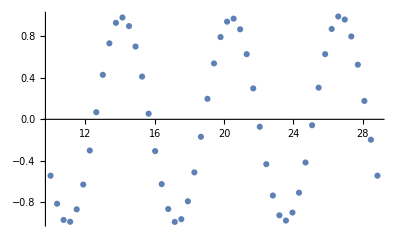
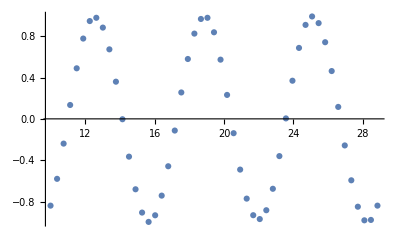

```mathematica
solverDE[eqs[1],{ϕ1,ϕ2},{x,10},1];
ListPlot/@%
```

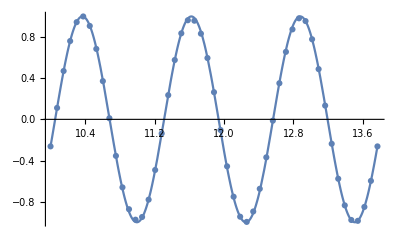

```mathematica
testFitting[eqs[5],{ϕ1,ϕ2},{x,10},5]
```

### Example 2: 2nd order ODE

```mathematica
DEs[ϕ_,x_,p_]:={-ϕ''[x]+V[x]ϕ[x]-p^2 ϕ[x]==0,ϕ[1]==1,ϕ'[1]==0};
V[x_]:=1/x
```

{InterpolatingFunction[{{1., 10.}}, <>]}

(0.433945-0.248122 ⅈ) ⅇ^(-100 ⅈ x)+(0.433945+0.248122 ⅈ) ⅇ^(100 ⅈ x)

0.519412

0.519412

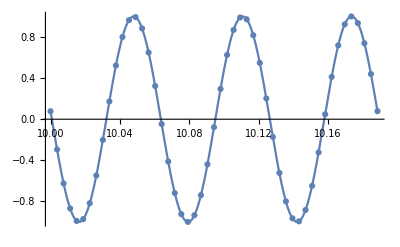

```mathematica
p=100;min=10;
waveL=N[(2π)/p];max=min+3waveL;
ϕ/.NDSolve[DEs[ϕ,x,p],ϕ,{x,1,10}]

data=solverDE[DEs[ϕ,x,p],{ϕ},{x,10},p][[1]];
fitExp[data,p][x]
findRealPhase[data,p]
phaseShift=findComplexPhase[data,p]

Show[ListPlot@data,Plot[Max@data[[;;,2]]Cos[p x+phaseShift],{x,min,max }]]

Clear[p,min,ν,phaseShift,waveL,max,data]
```

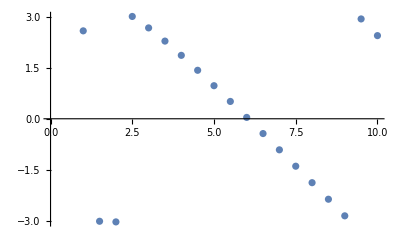

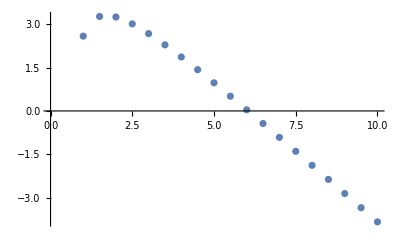

```mathematica
pRange=Range[1,10,0.5];
phaseTable[DEs[ϕ,x,p],{ϕ},x,{p,pRange}][[1]];
ListPlot[Transpose@{pRange,%}]
pPhaseTable[DEs[ϕ,x,p],{ϕ},x,{p,pRange}][[1]];
ListPlot[%]
Clear[pRange];
```